# Bulk Modulus

## structure factor

### load data

```mathematica
p0s={3.80,3.825,3.85};
 temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 recs=Table[Table[i,{i,0,9}],Length[p0s]];
tauEstimate={{1, 3, 4,8, 15, 40,70,150, 250, 600,2000 ,2500,4500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{2 ,4,10, 20, 40,60, 80,200, 500 ,800 ,1400, 2500 ,4200 ,5000, 6000,8500, 9500}};
```

```mathematica
Length[recs[[1]]]
```

11

```mathematica
sks=Table[Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/smallKSk_N4096_p","_T","_spacing","_idx","_rec",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,100000,tauEstimate[[p,T]]*100],records[[p,i]],recs[[p,rec]]},{3,4,8,0,0,0}],"Data"],{rec,Length[recs[[p]]]}],$Failed],{i,Length[records[[p]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec1.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/smallKSk_N4096_p3.8000_T0.06300000_spacing100000_idx14_rec2.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
sksMean=Table[Table[Table[Mean[Flatten[Table[DeleteCases[Table[sks[[p,T,i,time,2,rec]],{i,Length[sks[[p,T]]]}],_Missing|_Part|0.],{time,Length[recs]}]]],{rec,Max[Table[Length[sks[[p,T,i,1,1]]],{i,Length[sks[[p,T]]]}]]-1}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
sksMean[[1,2]]
```

{0.00667381,0.00609419,0.00653098,0.00589524,0.00342427,0.0109117,0.00634113,0.00952409,0.00638295,0.00828266,0.00853482,0.00762061,0.00753444,0.00709118,0.0107361,0.00735994,0.00869628,0.00485791,0.0117751,0.00915141,0.0077635,0.00753222,0.00722383,0.00567431,0.00805682,0.00970776,0.00910288,0.00551598,0.00845223,0.00971603,0.00961176,0.00587701,0.0076285,0.00555711,0.0116149,0.00531616,0.00817324,0.00697357,0.00775242,0.00615334,0.00699956,0.00697423,0.00689244,0.0104915,0.0129033,0.0074772,0.0070055,0.00911962,0.0101856,0.00935639,0.00785462,0.0081241,0.0076306,0.0105316,0.00678271,0.00722369,0.00879314,0.00742237,0.00939399,0.00490986,0.00949291,0.00811901,0.00941671,0.00623149,0.0150614,0.00924174,0.00687053,0.009107,0.0102201,0.00986862,0.0100195,0.00932225,0.00649832,0.00670077,0.0117362,0.00793882,0.00954363,0.010398,0.0103857,0.0108684,0.00850135,0.00934372,0.00818829,0.0119916,0.0109719,0.0104993,0.00882645,0.0108977,0.00906917,0.0106557,0.0110717,0.0146295,0.0112544,0.0115213,0.0127043,0.00790047,0.00819225,0.0134027,0.0083808,0.00982521,0.0151633,0.0141137,0.0151836,0.00853727,0.0127968,0.00804402,0.0119876,0.0169437,0.0133462,0.0102372,0.0164642,0.0137624,0.0206068,0.014376,0.014571,0.0151716,0.0178129,0.015775,0.0137746,0.0150446,0.0166545,0.010458,0.0169465,0.0176491,0.0180955,0.020118,0.0164464,0.0168299,0.0171067,0.0183329,0.0194351,0.0177504,0.0179722,0.015606,0.020788,0.014837,0.0198534,0.0154024,0.015897,0.0269441,0.0192737,0.0229252,0.0305972,0.0246139,0.020962,0.0166342,0.0201885,0.0193049,0.0266526,0.0210483,0.0257603,0.0208557,0.0235459,0.0187711,0.0305372,0.0301068,0.033737,0.0300847,0.0328434,0.0267338,0.0246386,0.0369451,0.0348277,0.0272772,0.024927,0.0356902,0.0369857,0.026765,0.0331397,0.0349036,0.0364014,0.0348452,0.0454749,0.0396333,0.042997,0.0461638,0.0279994,0.0366277,0.0304597,0.040722,0.0551052,0.0302357,0.0440096,0.0407658,0.0405401,0.0355184,0.0342258,0.043226,0.0454475,0.0510275,0.0498497,0.0528691,0.0470374,0.043713,0.0527301,0.0558261,0.0394589,0.0581508,0.0361608,0.0586245,0.0611787,0.0410728,0.0567365,0.130115,0.0528475,0.0662973,0.0426858,0.0630079,0.0782838,0.0756162,0.0690922,0.0530175,0.0776183,0.068539,0.06213,0.0801345,0.0482887,0.0933588,0.0536488,0.0624214,0.0737092,0.0755415,0.0952192,0.0666229,0.0632405,0.061871,0.0999384,0.0975751,0.0894425,0.10352,0.106598,0.095676,0.0687098,0.0976084,0.0698353,0.115702,0.177697,0.120234,0.0780642,0.104946,0.109461,0.117657,0.122193,0.101216,0.0820817,0.105706,0.130533,0.15744,0.191107,0.148443,0.119679,0.144997,0.174644,0.108071,0.178845,0.140749,0.210582,0.185445,0.163533,0.165341,0.158134,0.166092,0.164649,0.147077,0.172334,0.140778,0.191793,0.236547,0.160575,0.208148,0.199463,0.204606,0.17706,0.226731,0.266526,0.188687,0.241279,0.111323,0.189315,0.197438,0.312394,0.218606,0.211056,0.263485,0.245704,0.286037,0.188987,0.295679,0.264232,0.181243,0.275263,0.237457,0.235414,0.244261,0.319671,0.288302,0.256346,0.321927,0.317862,0.260761,0.357643,0.34667,0.322339,0.438348,0.347249,0.224663,0.361309,0.305959,0.295054,0.303642,0.262558,0.383022,0.33783,0.349023,0.315391,0.336901,0.344192,0.320407,0.217339,0.362339,0.304933,0.384556,0.455125,0.376645,0.314188,0.450922,0.485611,0.282515,0.50756,0.394296,0.482523,0.463785,0.54978,0.333398,0.331617,0.427594,0.347053,0.362694,0.39706,0.299459,0.33006,0.351438,0.484707,0.425219,0.332149,0.482,0.34983,0.487325,0.327503,0.313956,0.389716,0.517259,0.576315,0.501243,0.282709,0.5049,0.436664,0.487626,0.439763,0.40622,0.524202,0.425377,0.412856,0.350296,0.43607,0.580152,0.304108,0.594613,0.357008,0.53859,0.400252,0.489107,0.578593,0.395932,0.562671,0.411524,0.449348,0.407924,0.415123,0.512046,0.482559,0.473662,0.258725,0.443675,0.362249,0.34369,0.350418,0.428418,0.388697,0.577865,0.570975,0.473185,0.662505,0.382645,0.402642,0.423478,0.37601,0.489326,0.483465,0.441804,0.688553,0.370015,0.475974,0.413094,0.512915,0.445782,0.435592,0.531069,0.614263,0.775478,0.487543,0.581265,0.50307,0.366608,0.477755,0.429631,0.534925,0.56114,0.384816,0.511337,0.444785,0.521335,0.474656,0.564332,0.447312,0.500628,0.199297,0.508252,0.257262,0.420268,0.337518,0.572697,0.519726,0.408674,0.510867,0.366166,0.632371,0.642496,0.538897,0.461334,0.399363,0.422783,0.4911,0.409262,0.365307,0.472632,0.375108,0.459625,0.386826,0.472105,0.548104,0.456976,0.445476,0.573048,0.520368,0.524469,0.456243,0.515694,0.409773,0.74375,0.426754,0.489038,0.34675,0.519551,0.566135,0.452678,0.445538,0.434324,0.47342,0.416981,0.565631,0.46492,0.445873,0.485112,0.387282,0.479817,0.400515,0.530874,0.580637,0.499255,0.508239,0.369534,0.4966,0.45838,0.407082,0.511737,0.48999,0.378548,0.534945,0.512452,0.347851,0.3979,0.429835,0.834599,0.353385,0.471852,0.407586,0.58675,0.572253,0.517016,0.410363,0.497782,0.46593,0.597466,0.648483,0.416042,0.517137,0.517766,0.456271,0.591864,0.393129,0.47216,0.4668,0.50136,0.489212,0.495503,0.524415,0.546943,0.378087,0.528045,0.605661,0.358222,0.456683,0.605,0.449301,0.389394,0.506082,0.546449,0.462981,0.465479,0.399698,0.58835,0.512307,0.59196,0.460714,0.564809,0.585805,0.531202,0.384577,0.487205,0.47666,0.525959,0.660921,0.494891,0.604712,0.566316,0.388326,0.506761,0.242341,0.507228,0.416113,0.552147,0.549728,0.514719,0.511809,0.510822,0.568149,0.887201,0.777686,0.447995,0.478443,0.560419,0.537981,0.604361,0.661299,0.576997,0.648334,0.549813,0.456097,1.07578,0.573202,0.52949,0.565125,0.523461,0.716294,0.523308,0.447416,0.615484,0.441052,0.4156,0.522333,0.566976,0.449724,0.590112,0.686203,0.454507,0.615587,0.561149,0.732388,0.832064,0.608074,0.619812,0.509145,0.616522,0.503148,0.614795,0.513904,0.373747,0.553354,0.679099,0.597728,0.595867,0.936422,0.468397,0.733903,0.674328,0.524495,0.599664,0.525198,0.950973,0.764119,0.657644,0.619014,0.602907,0.610297,0.614702,0.589641,0.723548,0.462921,0.533117,0.880634,0.784908,0.641207,0.730111,0.515442,0.970244,0.779576,0.586777,0.774759,0.679784,0.769178,0.824723,1.02286,0.643182,0.634438,0.444131,0.683373,0.759927,0.861934,0.770953,0.705202,0.604024,0.709236,0.918773,0.608839,0.690227,0.792408,0.629983,0.876926,0.75749,0.617189,0.906313,0.714002,0.87816,0.641601,0.790749,0.772279,0.654139,0.689255,0.620581,0.732987,0.914542,0.849584,0.783697,0.731662,0.812786,0.810152,0.709588,0.614493,0.75048,0.631417,0.871945,0.882392,0.765896,0.594255,0.74987,0.994119,1.23758,1.04498,0.759119,0.902948,0.717301,0.724169,1.00322,1.15874,0.839694,0.729093,0.887695,0.929091,1.01653,0.908856,0.918422,0.763639,0.624451,1.22558,1.07198,0.768112,0.944436,0.78039,0.831081,0.891592,1.0537,1.03987,0.728353,1.02414,0.962214,1.03501,0.902286,0.984337,0.843962,1.1329,1.35382,1.0536,0.978738,1.05644,0.801619,1.13288,1.03693,0.975645,1.29893,1.14549,1.14245,0.942281,0.881104,0.891216,1.04646,1.20737,1.05131,1.29297,1.11901,1.34394,0.846107,1.11138,0.898314,1.20103,1.01621,1.16628,1.03232,1.35197,0.944699,1.3507,1.74393,1.29521,0.917047,1.29006,1.19892,1.10963,1.506,0.967042,1.22034,0.818991,0.88696,1.02695,1.14468,0.933581,1.27051,1.35652,1.18108,1.51313,1.06519,0.927877,0.69614,1.24135,1.27077,1.00994,1.96549,1.02902,1.57363,1.15562,1.21943,1.37476,1.26117,0.984273,1.1162,1.45741,1.07333,1.18996,0.949802,1.37826,1.32029,1.49217,1.1381,1.32031,1.4761,1.33174,1.07998,1.32603,1.19661,1.93835,1.74016,1.02703,1.45512,1.26347,1.67509,1.63496,1.41583,1.45736,1.27435,1.03461,1.3511,1.57645,1.74937,1.461,1.35651,1.29421,1.775,1.45192}

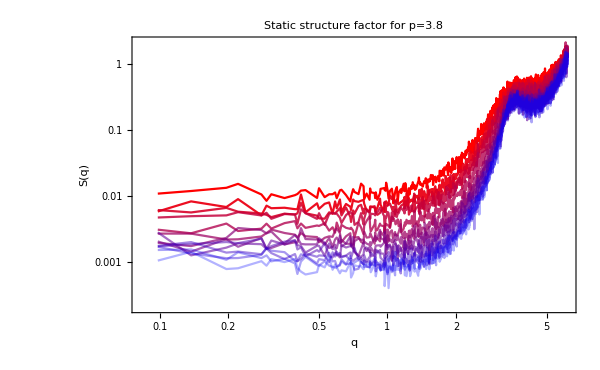
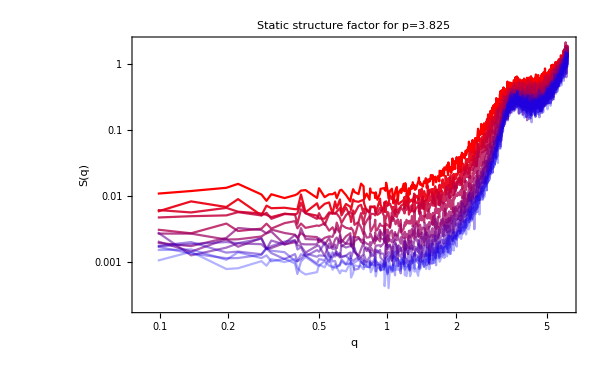
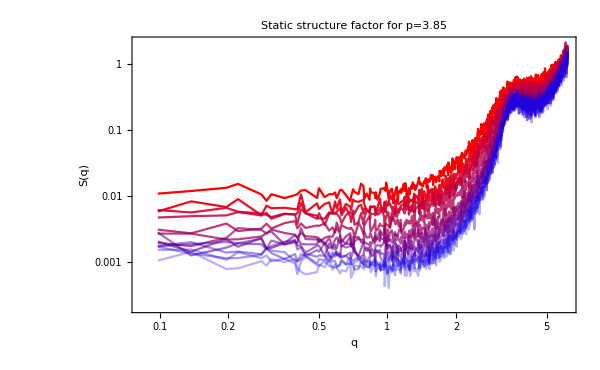

```mathematica
sqPLot=Table[ListLogLogPlot[Table[Table[{sks[[1,T,1,1,1,rec]],sksMean[[1,T,rec]]},{rec,Length[sksMean[[1,T]]]}],{T,Length[temperatures[[1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[1]]]],Joined->True,FrameLabel->{"q","S(q)"},PlotLabel->"Static structure factor for p="<>ToString[p0s[[p]]],ImageSize->600],{p,Length[p0s]}]
```

```mathematica
compressibility=Table[Table[Mean[Table[sksMean[[p,T,rec]],{rec,10}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0111993,0.00684327,0.00561129,0.00504123,0.00344256,0.00260575,0.00240209,0.00199662,0.00191822,0.00190497,0.00144988,0.00133998,0.00118769,0.00101434},{0.0109739,0.00696973,0.00601992,0.00344702,0.00263291,0.00221314,0.00194449,0.0016015,0.00137607,0.00119588,0.00103276,0.000874898,0.000762296},{0.00745356,0.00385531,0.00281359,0.00174197,0.00142237,0.00106853,0.000803808,0.000473021,0.000250819,0.00015879,0.000129207,0.0000717807,0.0000478869,0.0000364499,0.0000279442,0.0000259797,0.0000188595}}

```mathematica
compressibility={{0.011199273784966107,0.006843271602432324,0.005611288719792794,0.005041234977461774,0.0034425583850431754,0.0026057510940828517,0.002402093767504809,0.0019966246441788602,0.0019182227717051852,0.0019049662456268918,0.001449880590064925,0.0013399825929035518,0.001187690840811528,0.001014343011690452},{0.010973863616378617,0.006969729232530318,0.006019921555357807,0.0034470215575048853,0.0026329094381145244,0.0022131356244573337,0.0019444910237750798,0.0016014985435969943,0.0013760687245457778,0.001195880727373862,0.0010327648584341675,0.000874898354553366,0.0007622957395221339},{0.007453560814727081,0.0038553113302460763,0.0028135912408168745,0.0017419724263324672,0.0014223701929428829,0.0010685323178511355,0.0008038075411382475,0.00047302076751918546,0.0002508192704905529,0.00015879046536729807,0.0001292071964184393,0.00007178071005006233,0.00004788692408399204,0.00003644992471026816,0.000027944243002211488,0.000025979680020164673,0.00001885945885242752}};
```

```mathematica
fitting=NonlinearModelFit[Table[{temperatures[[1,T]],1/(compressibility[[T]]/temperatures[[1,T]])},{T,Length[temperatures[[1]]]}],{A*x^B},{A,B},x]
```

FittedModel[14.5064 x^0.294567]

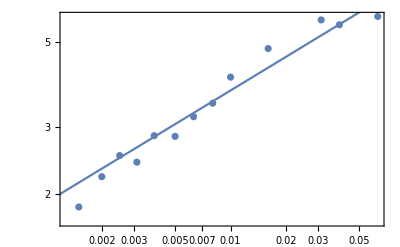

```mathematica
Show[ListLogLogPlot[Table[{temperatures[[1,T]],1/(compressibility[[T]]/temperatures[[1,T]])},{T,Length[temperatures[[1]]]}]],LogLogPlot[fitting[x],{x,0.000001,0.1}]]
```

## Numerical

### data loading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 records=Table[Table[i,{i,10,19}],Length[p0s]];
epsilons={{-0.001,0.,0.001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.825/isoCompression/timePressue_isoCompression_N4096_p3.8250_T0.00800000_epsilon0.00000000_idx10.nc"]
```

```mathematica
timePressure=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx12.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_idx15.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressure[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressureMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressure[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressure[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureMean
```

{{{{0.422435,0.433836,0.446251}},{{0.322941,0.333929,0.345035}},{{0.281129,0.291714,0.302406}},{{0.244687,0.254772,0.265014}},{{0.178785,0.187842,0.196946}},{{0.12188,0.129544,0.137061}},{{0.0990572,0.105768,0.112651}},{{0.0776427,0.0833365,0.0888063}},{{0.0593955,0.0642898,0.0682221}},{{0.0421304,0.0456132,0.0484917}},{{0.029454,0.0321637,0.0351424}},{{0.0240922,0.0270873,0.0302823}},{{0.0191463,0.0222616,0.0255752}},{{0.0145137,0.0174773,0.0214086}}},{{{0.368757,0.38051,0.391904}},{{0.275908,0.286473,0.297137}},{{0.237295,0.247382,0.25766}},{{0.145148,0.153837,0.162588}},{{0.0967217,0.104295,0.11187}},{{0.0781879,0.0851977,0.0922053}},{{0.0612173,0.0677694,0.0741582}},{{0.0474978,0.0534625,0.0593621}},{{0.0347663,0.0402149,0.0455359}},{{0.0262088,0.0313003,0.0362596}},{{0.0192835,0.0240272,0.028632}},{{0.0135299,0.0179894,0.0222536}},{{0.00785008,0.0119824,0.0158616}}},{{{0.231909,0.242287,0.252482}},{{0.114927,0.123061,0.13137}},{{0.0737175,0.0808885,0.0881134}},{{0.0340476,0.03994,0.0458253}},{{0.0242668,0.0298117,0.0353001}},{{0.0128329,0.0178257,0.0228266}},{{0.00873724,0.0134896,0.0182558}},{{0.00117457,0.00548879,0.00978234}},{{-0.00188092,0.00223054,0.00632159}},{{-0.00270104,0.00135252,0.00536283}},{{-0.00306612,0.000977688,0.00498945}},{{-0.00348997,0.000525444,0.00453321}},{{-0.00367279,0.000337077,0.00434656}},{{-0.00372655,0.000278862,0.00429957}},{{-0.00380967,0.000199681,0.00420753}},{{-0.00384064,0.000161359,0.0041756}},{{-0.00387737,0.000131308,0.00414086}}}}

```mathematica
pressurePlotS=Table[ListPlot[{Table[{timePressure[[1,T,1,1,1,1,i]],timePressure[[1,T,1,3,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}],Table[{timePressure[[1,T,1,3,1,1,i]],timePressure[[1,T,1,2,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}],Table[{timePressure[[1,T,1,3,1,1,i]],timePressure[[1,T,1,1,1,2,i]]},{i,1,Length[timePressure[[1,T,1,1,1,1]]],100}]},FrameLabel->{"t","P"},PlotStyle->redBluePlotConfig[3],PlotLabel->"T="<>ToString[temperatures[[1,T]]],Joined->True,ImageSize->300],{T,Length[temperatures[[1]]]}];
```

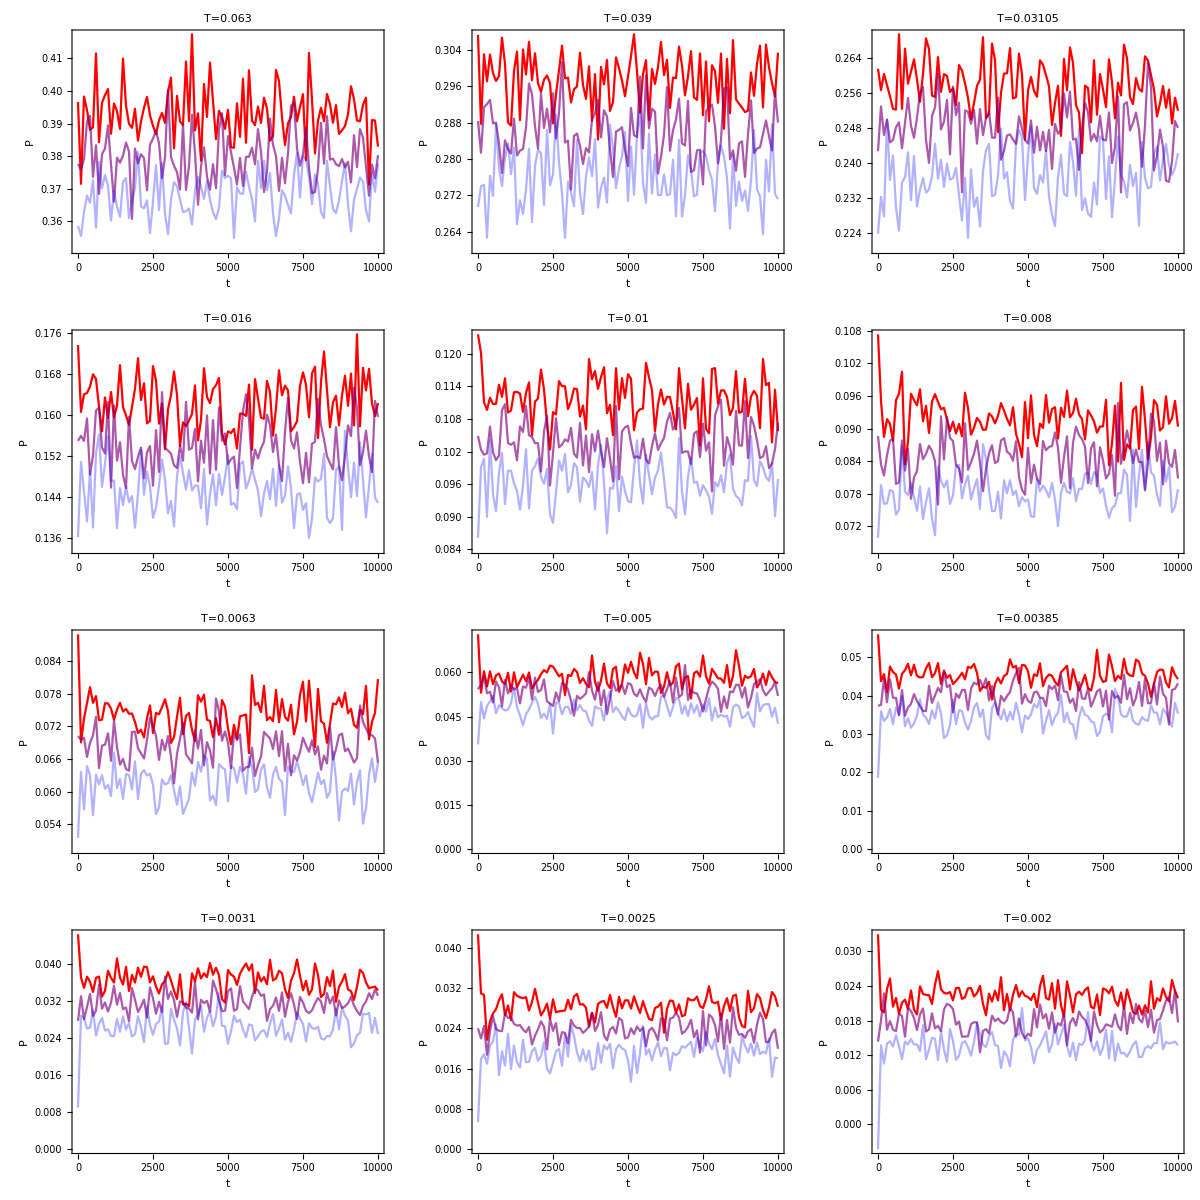

```mathematica
pressureTra=Grid[Partition[pressurePlotS,3]]
```

```mathematica
timePressureMean[[p,T,1,1]]
```

```mathematica
bulkModulus=Table[Table[(timePressureMean[[p,T,1,3]]-timePressureMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{5.95389,5.52358,5.31926,5.08188,4.54036,3.7952,3.39849,2.79091,2.20666,1.59032,1.42211,1.54752,1.60723,1.72373},{5.78675,5.30721,5.09104,4.3602,3.78716,3.50436,3.23523,2.96608,2.69242,2.5127,2.33714,2.18093,2.00287},{5.14308,4.11071,3.59895,2.94444,2.75832,2.49844,2.37965,2.15194,2.05063,2.01597,2.01389,2.00579,2.00484,2.00653,2.0043,2.00406,2.00456}}

```mathematica
bulkModulus=Table[-(Mean[Normal[timePressure[[1,T,1,1,1,2,100;;]]]]-Mean[Normal[timePressure[[1,T,1,3,1,2,100;;]]]])/2/0.001/2,{T,Length[temperatures[[1]]]}]
```

{5.76025,5.32531,5.07099,4.3956,3.82426,3.52433,3.2383,2.95894,2.66836,2.45754,2.29538,2.16032,2.02998}

```mathematica
fittingNumerical=NonlinearModelFit[Table[{temperatures[[1,T]],bulkModulus[[T]]},{T,Length[temperatures[[1]]]}],{A*x^B},{A,B},x]
```

FittedModel[13.1584 x^0.280852]

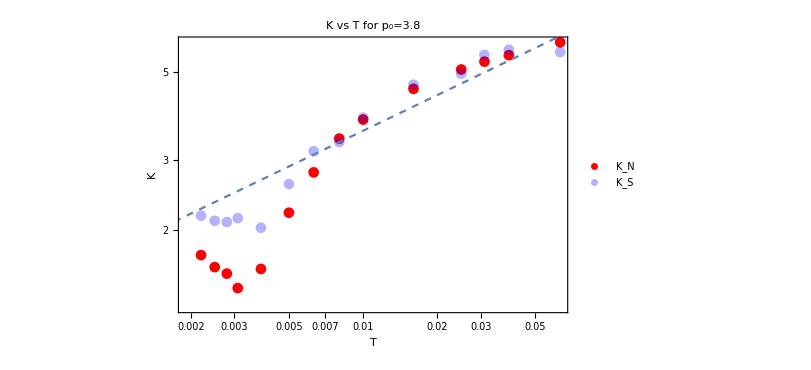
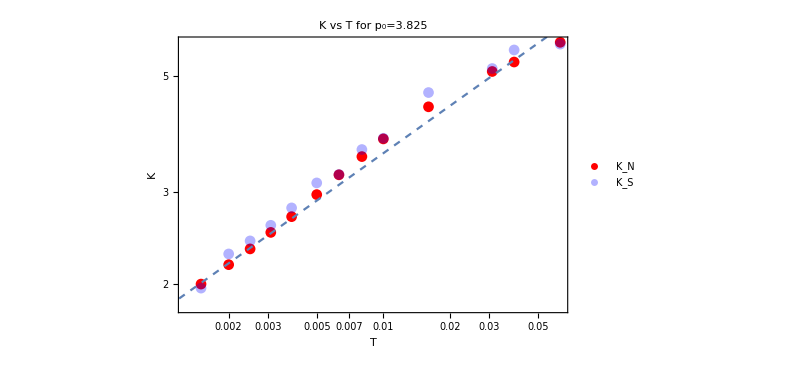
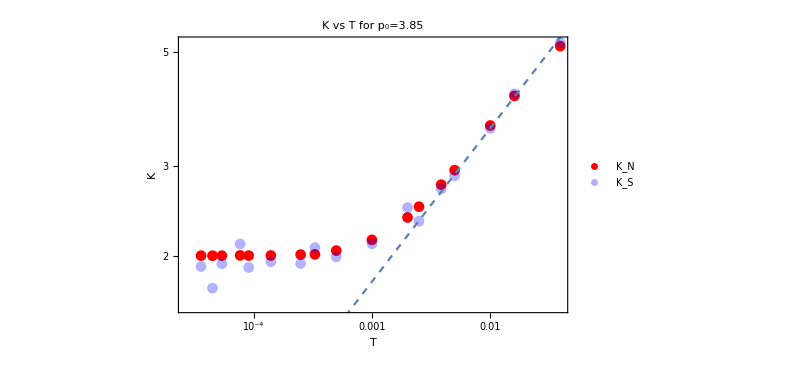

```mathematica
kPLots=Table[Show[ListLogLogPlot[{Table[{temperatures[[p,T]],bulkModulus[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],1/(compressibility[[p,T]]/temperatures[[p,T]])},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[2],PlotLegends->{"K_N","K_S"}],LogLogPlot[14.158x^0.3,{x,0.000001,0.1},PlotStyle->Dashed]],{p,Length[p0s]}]
```

```mathematica
results=Table[Grid[Partition[{sqPLot[[p]],kPLots[[p]]},2]],{p,Length[p0s]}]
```

{-Graphics- | -Graphics-,-Graphics- | -Graphics-,-Graphics- | -Graphics-}

```mathematica
Table[Export["/home/chengling/Research/updates/05162024/bulkModulus"<>ToString[p0s[[p]]]<>".jpeg",results[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05162024/bulkModulus3.8.jpeg,/home/chengling/Research/updates/05162024/bulkModulus3.825.jpeg,/home/chengling/Research/updates/05162024/bulkModulus3.85.jpeg}

```mathematica
Export["/home/chengling/Research/updates/05092024/kPLots.jpeg",kPLots,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/kPLots.jpeg

```mathematica
Export["/home/chengling/Research/updates/05092024/SqPlot.jpeg",sqPLot,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/SqPlot.jpeg

## larger ϵ

```mathematica
test=Import["/home/chengling/Downloads/timePressue_N4096_p3.8250_T0.06300000_epsilon0.05000000_idx10.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

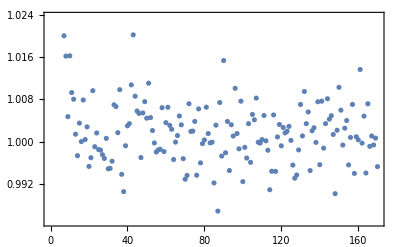

```mathematica
ListPlot[Table[{test[[1,i]],test[[2,i]]},{i,Length[test[[1]]]}]]
```

### smaller ϵ

### data loading

```mathematica
p0s={3.80}
```

{3.8}

```mathematica
temperatures={{00.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022}};
 records=Table[Table[i,{i,10,14}],Length[p0s]];
epsilons={{-0.001,0.,0.001},{-0.0001,0.,0.0001},{-0.00001,0.,0.00001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Normal[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_idx11.nc","Data"][[2,1;;10]]]
```

{0.0977089,0.0940092,0.0905322,0.0853599,0.086355,0.0931903,0.0997028,0.0911366,0.0882095,0.0934777}

```mathematica
Normal[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00010000_idx11.nc","Data"][[2,1;;10]]]
```

{0.0810542,0.0843894,0.0859837,0.0820457,0.0822349,0.0848988,0.0897095,0.0832979,0.0816164,0.0880473}

```mathematica
timePressureAreaLowT=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA1.0000_KP0.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon-0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00000000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_KA1.0000_KP0.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaLowT[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressurePeriLowT=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA0.0000_KP1.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon-0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00000000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.00630000_epsilon0.00100000_KA0.0000_KP1.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaLowTMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressureAreaLowT[[p,T,ep,epi,rec,2,100;;]]]],{rec,Length[timePressureAreaLowT[[p,T,ep,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureAreaLowTMean
```

{{{{-0.00144368,0.0025054,0.00645362},{0.00211018,0.0025054,0.00289917},{0.00246483,0.0025054,0.00254526}},{{-0.00189261,0.00205496,0.00599583},{0.00166165,0.00205496,0.00244889},{0.00201634,0.00205496,0.00209388}},{{-0.00230927,0.00163236,0.00556883},{0.00124006,0.00163236,0.0020234},{0.0015921,0.00163236,0.00167426}},{{-0.00259977,0.00133148,0.00527305},{0.000942395,0.00133148,0.00172747},{0.00129882,0.00133148,0.00137278}},{{-0.00272235,0.00121418,0.00516026},{0.000824262,0.00121418,0.00161268},{0.00118027,0.00121418,0.00125868}},{{-0.00284426,0.00110095,0.00505295},{0.000703312,0.00110095,0.00149482},{0.00106025,0.00110095,0.00113819}},{{-0.00296533,0.00097994,0.00494397},{0.000587997,0.00097994,0.00137741},{0.000943839,0.00097994,0.00102406}}}}

```mathematica
timePressurePeriLowTMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressurePeriLowT[[p,T,ep,epi,rec,2,100;;]]]],{rec,Length[timePressurePeriLowT[[p,T,ep,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressurePeriLowTMean
```

```mathematica
{{{{0.07906938699742307,0.08085538437184953,0.08233544172286074},{0.08065373142508657,0.08085538437184953,0.08085233060852243},{0.08075531147262649,0.08085538437184953,0.08083832870324859}},{{0.061288592995715596,0.062322804105488974,0.06242185480159304},{0.06232720382590027,0.062322804105488974,0.062355901889091236},{0.062353874072793795,0.062322804105488974,0.06236295557652198}},{{0.04423404996124854,0.04403304674631475,0.04329183966084848},{0.04415878351043161,0.04403304674631475,0.043797394971038565},{0.043959223494953625,0.04403304674631475,0.04420970389720612}},{{0.03199895473505895,0.03061029291610294,0.029892078180032103},{0.03102810544611785,0.03061029291610294,0.03062791830693571},{0.03111207759202674,0.03061029291610294,0.03064919586947573}},{{0.026804002196563193,0.025659193748644032,0.025166039180709494},{0.02607878755477542,0.025659193748644032,0.0259211497009582},{0.026146096111457046,0.025659193748644032,0.026039015898327494}},{{0.02194745782342335,0.021205154634139127,0.0209941357582334},{0.021117713410712755,0.021205154634139127,0.02115027332175218},{0.02119240375128361,0.021205154634139127,0.021074842405703585}},{{0.017326167035829593,0.016367823266489293,0.016804078656910318},{0.016715566446924526,0.016367823266489293,0.01647987263768877},{0.016663276686502283,0.016367823266489293,0.016743634363136296}}}}
```

{{{{0.0790694,0.0808554,0.0823354},{0.0806537,0.0808554,0.0808523},{0.0807553,0.0808554,0.0808383}},{{0.0612886,0.0623228,0.0624219},{0.0623272,0.0623228,0.0623559},{0.0623539,0.0623228,0.062363}},{{0.044234,0.044033,0.0432918},{0.0441588,0.044033,0.0437974},{0.0439592,0.044033,0.0442097}},{{0.031999,0.0306103,0.0298921},{0.0310281,0.0306103,0.0306279},{0.0311121,0.0306103,0.0306492}},{{0.026804,0.0256592,0.025166},{0.0260788,0.0256592,0.0259211},{0.0261461,0.0256592,0.026039}},{{0.0219475,0.0212052,0.0209941},{0.0211177,0.0212052,0.0211503},{0.0211924,0.0212052,0.0210748}},{{0.0173262,0.0163678,0.0168041},{0.0167156,0.0163678,0.0164799},{0.0166633,0.0163678,0.0167436}}}}

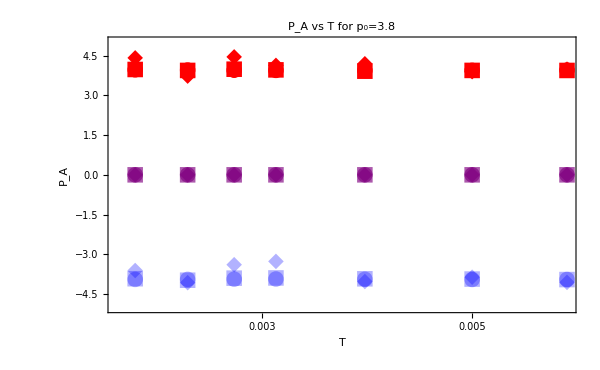

```mathematica
areaPressureLowTPlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,3]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,2]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,1,1]]-timePressureAreaLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_A"},ImageSize->600,PlotLabel->"P_A vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->{All,{-5,5}},PlotMarkers->{{"●",16},{"●",16},{"●",16}}],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,3]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,2]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,2,1]]-timePressureAreaLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotMarkers->{{"■",16},{"■",16},{"■",16}}],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,3]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,2]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressureAreaLowTMean[[p,T,3,1]]-timePressureAreaLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotMarkers->{{"◆",16},{"◆",16},{"◆",16}}]],{p,Length[p0s]}];
Column[areaPressureLowTPlots]
```

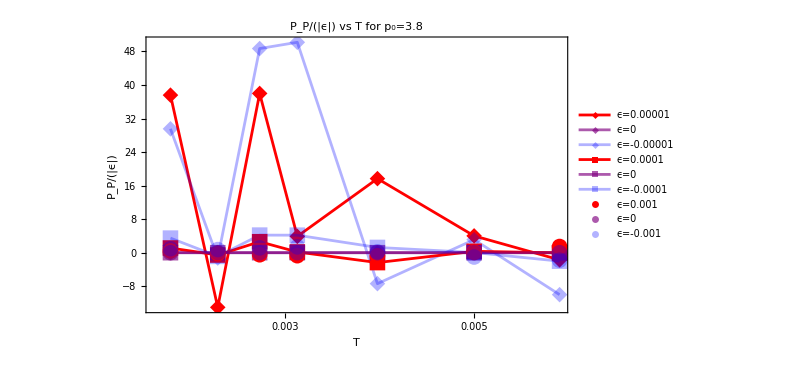

```mathematica
periPressureLowTPlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,3]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,2]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,3,1]]-timePressurePeriLowTMean[[p,T,3,2]])/epsilons[[3,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_P/(|ϵ|)"},ImageSize->600,PlotLabel->"P_P/(|ϵ|) vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.00001","ϵ=0","ϵ=-0.00001"},PlotMarkers->{{"◆",16},{"◆",16},{"◆",16}},Joined->True],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,3]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,2]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,2,1]]-timePressurePeriLowTMean[[p,T,2,2]])/epsilons[[2,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.0001","ϵ=0","ϵ=-0.0001"},PlotMarkers->{{"■",16},{"■",16},{"■",16}},Joined->True],ListLogLinearPlot[{Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,3]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,2]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],(timePressurePeriLowTMean[[p,T,1,1]]-timePressurePeriLowTMean[[p,T,1,2]])/epsilons[[1,3]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.001","ϵ=0","ϵ=-0.001"},PlotMarkers->{{"●",16},{"●",16},{"●",16}}]],{p,Length[p0s]}];
Column[periPressureLowTPlots]
```

```mathematica
Export["/home/chengling/Research/updates/05232024/LowTPressue.jpeg",Grid[Partition[{areaPressureLowTPlots[[1]],periPressureLowTPlots[[1]]},2]],ImageResolution->800]
```

/home/chengling/Research/updates/05232024/LowTPressue.jpeg

## A, P contributions

### data loading

```mathematica
p0s={3.80,3.825,3.85}
```

{3.8,3.825,3.85}

```mathematica
temperatures={{0.063, 0.039 ,0.03105,0.025, 0.016, 0.01, 0.008 ,0.0063 ,0.005 ,0.00385 ,0.0031 ,0.0028,0.0025 ,0.0022},{0.063,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015},{0.039 ,0.016 ,0.01 ,0.005 ,0.00385 ,0.0025 ,0.002, 0.001 ,0.0005, 0.00033, 0.00025, 0.00014 ,0.000091 ,0.000077,0.000054, 0.000045 ,0.000036}};
 records=Table[Table[i,{i,10,14}],Length[p0s]];
epsilons={{-0.001,0.,0.001}};
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.825/isoCompression/timePressue_isoCompression_N4096_p3.8250_T0.00800000_epsilon0.00000000_KA1.0000_KP0.0000_idx11.nc"]
```

{/firstValue,/secondValue}

```mathematica
timePressureArea=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA1.0000_KP0.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA1.0000_KP0.0000_idx10.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA1.0000_KP0.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureArea[[1,1,1,1]]
```

{<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>,<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>}

```mathematica
timePressurePeri=Table[Table[
Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p","/isoCompression/timePressue_isoCompression_N4096_p","_T","_epsilon","_KA0.0000_KP1.0000_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],epsilons[[ep,epi]],records[[p,rec]]},{3,4,8,8,0}],"Data"],{rec,Length[records[[p]]]}],$Failed],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon-0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::format: Cannot import data as Data.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA0.0000_KP1.0000_idx10.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/bulkModulus/p3.800/isoCompression/timePressue_isoCompression_N4096_p3.8000_T0.06300000_epsilon0.00100000_KA0.0000_KP1.0000_idx11.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
timePressureAreaMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressureArea[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressureArea[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressureAreaMean
```

{{{{0.0140905,0.0180315,0.0219718}},{{0.0080024,0.0119483,0.0158958}},{{0.00586672,0.00981674,0.0137672}},{{0.00419569,0.0081446,0.0120945}},{{0.00159747,0.00554998,0.0095068}},{{-0.000237873,0.0037165,0.00767001}},{{-0.000878947,0.00307181,0.00702349}},{{-0.00144368,0.0025054,0.00645362}},{{-0.00189261,0.00205496,0.00599583}},{{-0.00230927,0.00163236,0.00556883}},{{-0.00259977,0.00133148,0.00527305}},{{-0.00272235,0.00121418,0.00516026}},{{-0.00284426,0.00110095,0.00505295}},{{-0.00296533,0.00097994,0.00494397}}},{{{0.014429,0.0183947,0.0223345}},{{0.00834015,0.0122811,0.0162313}},{{0.00618756,0.0101336,0.0140804}},{{0.00187662,0.00583121,0.00978733}},{{0.0000246569,0.0039824,0.00794298}},{{-0.000624536,0.00333399,0.00729838}},{{-0.00119532,0.00276686,0.00673267}},{{-0.00165008,0.00231563,0.00628325}},{{-0.00207096,0.00189756,0.00586778}},{{-0.00236025,0.00161179,0.00558379}},{{-0.00260262,0.00137101,0.00534516}},{{-0.00281613,0.00115843,0.00513513}},{{-0.00304721,0.000931776,0.00491299}}},{{{0.00870436,0.0126411,0.0165781}},{{0.00217335,0.00612192,0.010076}},{{0.000276245,0.00423507,0.0081956}},{{-0.00146175,0.00250685,0.00648034}},{{-0.00190784,0.00206582,0.00604389}},{{-0.00247921,0.00150064,0.00548514}},{{-0.00271311,0.00127045,0.00525777}},{{-0.00324753,0.000744028,0.00473865}},{{-0.00357632,0.000419174,0.00441828}},{{-0.0037054,0.000291455,0.00429198}},{{-0.00377063,0.000226765,0.00422777}},{{-0.00386567,0.000132148,0.00413375}},{{-0.00391039,0.0000874222,0.00408936}},{{-0.00392342,0.0000744125,0.0040762}},{{-0.00394524,0.0000526859,0.00405456}},{{-0.00395383,0.0000440271,0.00404601}},{{-0.00396257,0.0000353738,0.00403728}}}}

```mathematica
timePressurePeriMean=Table[Table[
Table[Table[Mean[Table[Mean[Normal[timePressurePeri[[p,T,1,epi,rec,2,100;;]]]],{rec,Length[timePressurePeri[[p,T,1,epi]]]}]],{epi,Length[epsilons[[ep]]]}],{ep,Length[epsilons]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
timePressurePeriMean
```

{{{{0.408374,0.416186,0.424312}},{{0.314931,0.321953,0.329143}},{{0.275211,0.281912,0.288684}},{{0.240518,0.246634,0.252887}},{{0.177215,0.182322,0.187489}},{{0.12214,0.125925,0.129319}},{{0.0999876,0.102784,0.105471}},{{0.0790694,0.0808554,0.0823354}},{{0.0612886,0.0623228,0.0624219}},{{0.044234,0.044033,0.0432918}},{{0.031999,0.0306103,0.0298921}},{{0.026804,0.0256592,0.025166}},{{0.0219475,0.0212052,0.0209941}},{{0.0173262,0.0163678,0.0168041}}},{{{0.354087,0.36217,0.369782}},{{0.267651,0.274199,0.281031}},{{0.231075,0.237263,0.243512}},{{0.143256,0.14796,0.152833}},{{0.0967254,0.10032,0.103979}},{{0.0788124,0.0818662,0.0849615}},{{0.0624381,0.0649832,0.067463}},{{0.0490592,0.0511081,0.0530988}},{{0.0368705,0.0383402,0.0396621}},{{0.0285322,0.029657,0.0305898}},{{0.0219189,0.0227605,0.0231763}},{{0.0163812,0.0167821,0.0170285}},{{0.0108706,0.0110116,0.0111103}}},{{{0.223326,0.22959,0.235857}},{{0.11273,0.116922,0.121317}},{{0.0734375,0.0766399,0.0799393}},{{0.0355214,0.0374348,0.0393668}},{{0.02616,0.0277562,0.0292434}},{{0.0153255,0.0163246,0.0173089}},{{0.011454,0.0122097,0.0130124}},{{0.00443139,0.00475465,0.00502837}},{{0.00170007,0.00180452,0.00188154}},{{0.000992053,0.00104762,0.0010635}},{{0.000698839,0.000760108,0.000752303}},{{0.000369896,0.000386916,0.000398994}},{{0.000234301,0.000237081,0.000269536}},{{0.000186147,0.000205235,0.000214325}},{{0.000129685,0.000151084,0.000163199}},{{0.000107793,0.000118776,0.000145319}},{{0.0000830756,0.0000973155,0.000102743}}}}

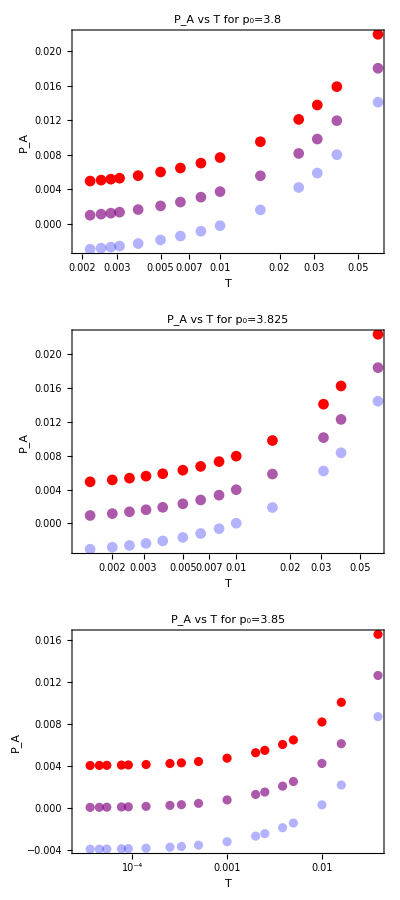

```mathematica
areaPressurePlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,3]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressureAreaMean[[p,T,1,1]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_A"},ImageSize->600,PlotLabel->"P_A vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All]],{p,Length[p0s]}];
Column[areaPressurePlots]
```

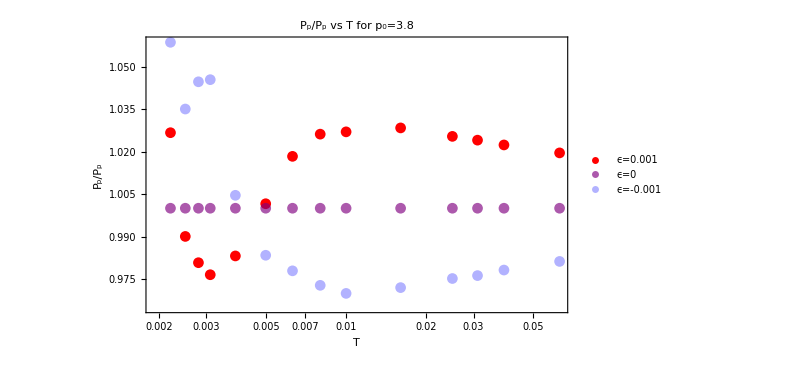
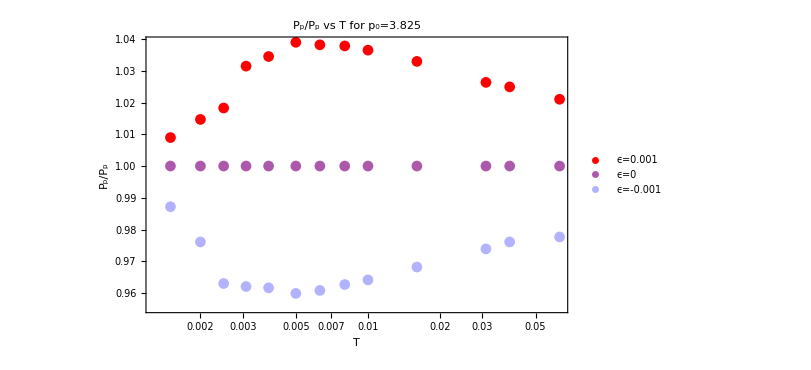
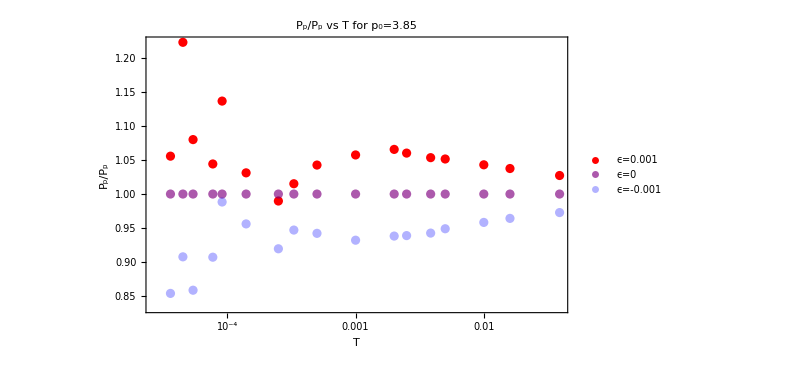

```mathematica
periPressurePlots=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,3]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,2]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],timePressurePeriMean[[p,T,1,1]]/timePressurePeriMean[[p,T,1,2]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","P_p/P_p"},ImageSize->600,PlotLabel->"P_p/P_p vs T for p_0="<>ToString[p0s[[p]]],PlotStyle->redBluePlotConfig[3],PlotRange->All,PlotLegends->{"ϵ=0.001","ϵ=0","ϵ=-0.001"}]],{p,Length[p0s]}];
Column[periPressurePlots]
```

```mathematica
bulkModulusArea=Table[Table[(timePressureAreaMean[[p,T,1,3]]-timePressureAreaMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.97033,1.97335,1.97513,1.97469,1.97733,1.97697,1.97561,1.97433,1.97211,1.96953,1.9682,1.97065,1.9743,1.97733},{1.97637,1.9728,1.97322,1.97768,1.97958,1.98073,1.982,1.98333,1.98468,1.98601,1.98694,1.98781,1.99005},{1.96843,1.97566,1.97984,1.98552,1.98793,1.99109,1.99272,1.99655,1.99865,1.99934,1.9996,1.99986,1.99994,1.99991,1.99995,1.99996,1.99996}}

```mathematica
bulkModulusPeri=Table[Table[(timePressurePeriMean[[p,T,1,3]]-timePressurePeriMean[[p,T,1,1]])/2/0.001/2,{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{3.98455,3.55301,3.36809,3.09234,2.5685,1.79459,1.37081,0.816514,0.283315,-0.235553,-0.526719,-0.409491,-0.238331,-0.130522},{3.92357,3.34493,3.10909,2.39436,1.8135,1.53728,1.25623,1.00989,0.697894,0.514401,0.314362,0.161834,0.0599226},{3.13279,2.14667,1.62545,0.961345,0.77085,0.495848,0.389603,0.149245,0.0453676,0.0178629,0.013366,0.00727436,0.00880882,0.00704454,0.00837866,0.00938152,0.00491682}}

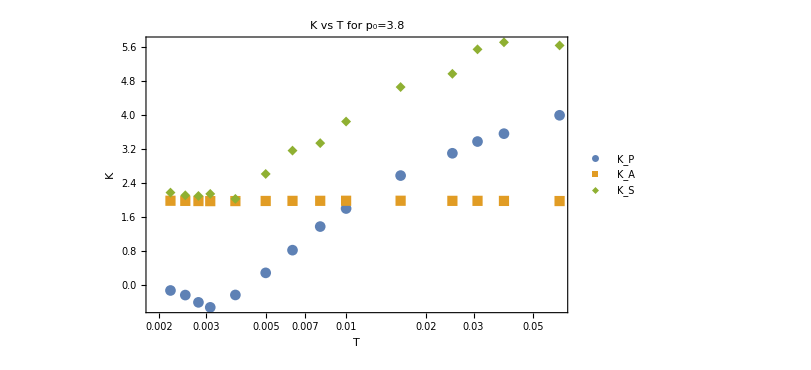
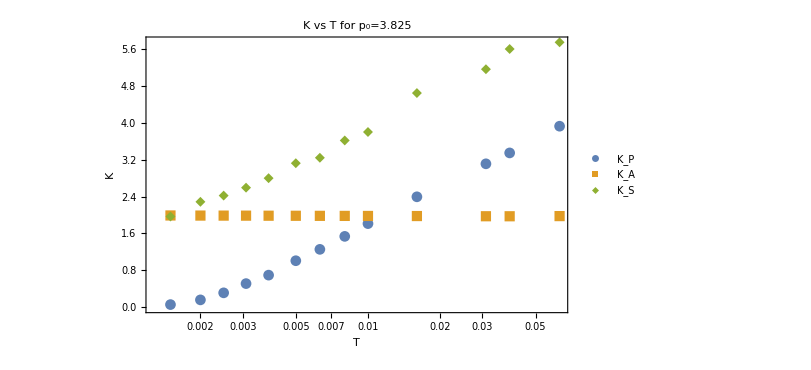
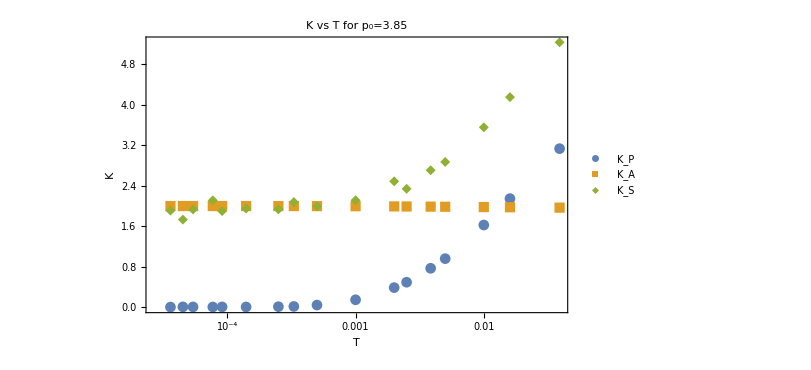

```mathematica
modulusPlot=Table[Show[ListLogLinearPlot[{Table[{temperatures[[p,T]],bulkModulusPeri[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],bulkModulusArea[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],1/(compressibility[[p,T]]/temperatures[[p,T]])},{T,Length[temperatures[[p]]]}]},FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotMarkers->Automatic,PlotLegends->{"K_P","K_A","K_S"}]],{p,Length[p0s]}]
```

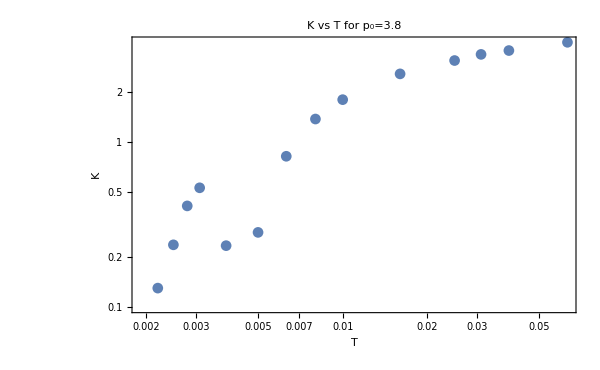
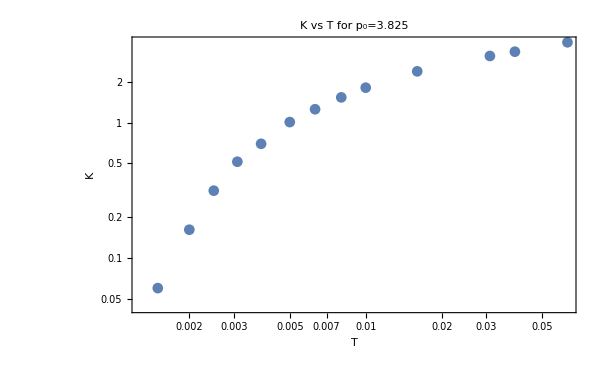
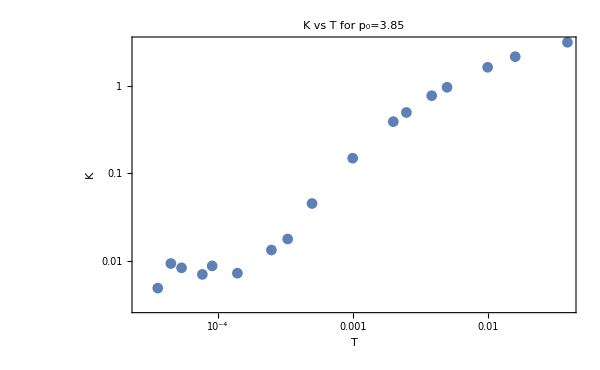

```mathematica
modulusKPPlots=Table[Show[ListLogLogPlot[Table[{temperatures[[p,T]],Abs[bulkModulusPeri[[p,T]]]},{T,Length[temperatures[[p]]]}],FrameLabel->{"T","K"},ImageSize->600,PlotLabel->"K vs T for p_0="<>ToString[p0s[[p]]],PlotMarkers->Automatic]],{p,Length[p0s]}]
```

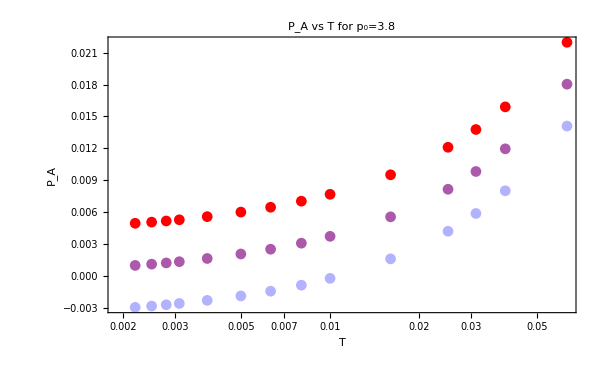
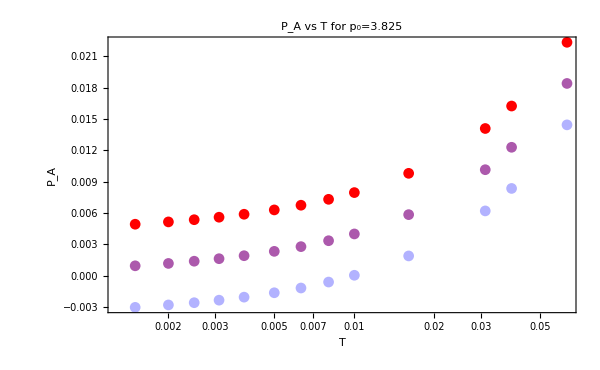
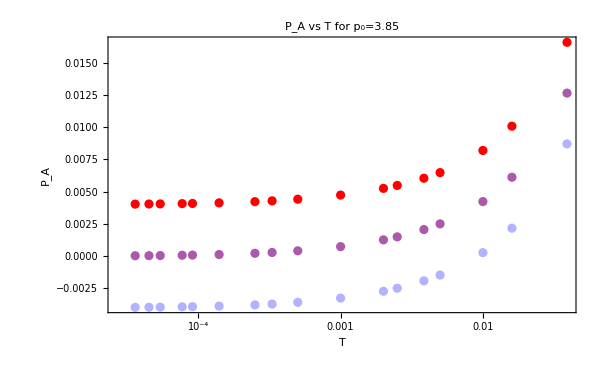
{-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-,-Graphics- | -Graphics-
-Graphics- | -Graphics-}

```mathematica
bulkModulusresults=Table[ Grid[Partition[{periPressurePlots[[p]],areaPressurePlots[[p]],modulusPlot[[p]],modulusKPPlots[[p]]},2]],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/05232024/bulkModulus"<>ToString[p0s[[p]]]<>".jpeg",bulkModulusresults[[p]],ImageResolution->800],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/05232024/bulkModulus3.8.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.825.jpeg,/home/chengling/Research/updates/05232024/bulkModulus3.85.jpeg}